```mathematica
(*Columbic interaction of charge*)
```

```mathematica
ClearAll["Global`*"]
```

```mathematica
Assumptions->{Im[α]==0,Im[β]==0,Re[α]>0,Re[β]>0}
```

Assumptions→{Im[α]==0,Im[β]==0,Re[α]>0,Re[β]>0}

```mathematica
rhoA[r_]:=α^3 Exp[- α r]/(8 Pi)
rhoA[r]
```

(ⅇ^(-r α) α^3)/(8 π)

```mathematica
}
```

```mathematica
rhoB[r_]:=β^3 Exp[-β r]/(8 Pi)
rhoB[r]
```

(ⅇ^(-r β) β^3)/(8 π)

```mathematica
phiA[r_]:=4Pi((1/r )Integrate[rhoA[x] x^2,{x,0,r}]+Integrate[x rhoA[x],{x,r,Infinity},Assumptions->{Im[α]==0,Im[β]==0,Re[α]>0,Re[β]>0}])
```

```mathematica
phiA[r]//Expand
```

1/r-ⅇ^(-r α)/r-1/2 ⅇ^(-r α) α

```mathematica
V1=2Pi((Integrate[r^2 rhoB[r]*Integrate[1/Sqrt[r^2+R^2-2r R x],{x,-1,1}],{r,0,Infinity},Assumptions->{Im[r]==0,Im[R]==0,Re[R]>0,Re[r]≥0,Im[α]==0,Im[β]==0,Re[α]>0,Re[β]>0}]))//Simplify
```

(ⅇ^(-R β) (-2+2 ⅇ^(R β)-R β))/(2 R)

```mathematica
V1E=V1/.{B->A,β->α}
```

(ⅇ^(-R α) (-2+2 ⅇ^(R α)-R α))/(2 R)

```mathematica
V2=-2Pi(Integrate[r Exp[-α r]*Integrate[rhoB[Sqrt[r^2+R^2-2r R x]],{x,-1,1}],{r,0,Infinity},Assumptions->{Im[r]==0,Im[R]==0,Re[R]>0,Re[r]≥0,Im[α]==0,Im[β]==0,Re[α]>0,Re[β]>0}])
```

-(ⅇ^(-R (α+2 β)) β^3 (ⅇ^(R (α+β)) R α^2+2 ⅇ^(2 R β) β-2 ⅇ^(R (α+β)) β-ⅇ^(R (α+β)) R β^2))/(2 R (α-β)^2 (α+β)^2)

```mathematica
V2//Simplify
```

(ⅇ^(-R (α+2 β)) β^3 (-2 ⅇ^(2 R β) β+ⅇ^(R (α+β)) (2 β+R (-α^2+β^2))))/(2 R (α-β)^2 (α+β)^2)

```mathematica
V2E=Limit[V2,{β->α}]
```

{-1/8 ⅇ^(-R α) α (1+R α)}

```mathematica
V2E//Simplify
```

{-1/8 ⅇ^(-R α) α (1+R α)}

```mathematica
V3=-2Pi α/(2 ) (Integrate[r^2 rhoB[r]*Integrate[Exp[-α Sqrt[r^2+R^2-2r R x]],{x,-1,1}],{r,0,Infinity},Assumptions->{Im[r]==0,Im[R]==0,Re[R]>0,Re[r]≥0,Im[α]==0,Im[β]==0,Re[α]>0,Re[β]>0}])
```

1/(8 R α (α-β)^3 (α+β)^3)ⅇ^(-2 R (α+β)-R (2 α+β)) β^3 (3 ⅇ^(2 R (2 α+β)) α^4-3 ⅇ^(R β+R (2 α+β)) α^4-2 ⅇ^(2 R (2 α+β)) R α^5-4 ⅇ^(R β+R (2 α+β)) R α^5-2 ⅇ^(R β+R (2 α+β)) R^2 α^6+8 ⅇ^(2 R (2 α+β)) α^3 β+8 ⅇ^(R β+R (2 α+β)) α^3 β-16 ⅇ^(R (2 α+β)+R (α+2 β)) α^3 β-3 ⅇ^(2 R (2 α+β)) R α^4 β+7 ⅇ^(R β+R (2 α+β)) R α^4 β-4 ⅇ^(R (2 α+β)+R (α+2 β)) R α^4 β+2 ⅇ^(R β+R (2 α+β)) R^2 α^5 β+6 ⅇ^(2 R (2 α+β)) α^2 β^2-6 ⅇ^(R β+R (2 α+β)) α^2 β^2+2 ⅇ^(2 R (2 α+β)) R α^3 β^2+2 ⅇ^(R β+R (2 α+β)) R α^3 β^2+4 ⅇ^(R β+R (2 α+β)) R^2 α^4 β^2+4 ⅇ^(2 R (2 α+β)) R α^2 β^3-8 ⅇ^(R β+R (2 α+β)) R α^2 β^3+4 ⅇ^(R (2 α+β)+R (α+2 β)) R α^2 β^3-4 ⅇ^(R β+R (2 α+β)) R^2 α^3 β^3-ⅇ^(2 R (2 α+β)) β^4+ⅇ^(R β+R (2 α+β)) β^4+2 ⅇ^(R β+R (2 α+β)) R α β^4-2 ⅇ^(R β+R (2 α+β)) R^2 α^2 β^4-ⅇ^(2 R (2 α+β)) R β^5+ⅇ^(R β+R (2 α+β)) R β^5+2 ⅇ^(R β+R (2 α+β)) R^2 α β^5+2 ⅇ^(2 R (α+β)) R α^5 Cosh[R α]^2+2 ⅇ^(2 R (α+β)) R^2 α^6 Cosh[R α]^2-4 ⅇ^(2 R (α+β)) R α^4 β Cosh[R α]^2-2 ⅇ^(2 R (α+β)) R^2 α^5 β Cosh[R α]^2-4 ⅇ^(2 R (α+β)) R^2 α^4 β^2 Cosh[R α]^2+4 ⅇ^(2 R (α+β)) R α^2 β^3 Cosh[R α]^2+4 ⅇ^(2 R (α+β)) R^2 α^3 β^3 Cosh[R α]^2-2 ⅇ^(2 R (α+β)) R α β^4 Cosh[R α]^2+2 ⅇ^(2 R (α+β)) R^2 α^2 β^4 Cosh[R α]^2-2 ⅇ^(2 R (α+β)) R^2 α β^5 Cosh[R α]^2-6 ⅇ^(2 R (α+β)) α^4 Cosh[R α] Sinh[R α]-4 ⅇ^(2 R (α+β)) R α^5 Cosh[R α] Sinh[R α]+16 ⅇ^(2 R (α+β)) α^3 β Cosh[R α] Sinh[R α]+6 ⅇ^(2 R (α+β)) R α^4 β Cosh[R α] Sinh[R α]-12 ⅇ^(2 R (α+β)) α^2 β^2 Cosh[R α] Sinh[R α]+4 ⅇ^(2 R (α+β)) R α^3 β^2 Cosh[R α] Sinh[R α]-8 ⅇ^(2 R (α+β)) R α^2 β^3 Cosh[R α] Sinh[R α]+2 ⅇ^(2 R (α+β)) β^4 Cosh[R α] Sinh[R α]+2 ⅇ^(2 R (α+β)) R β^5 Cosh[R α] Sinh[R α]-6 ⅇ^(2 R (α+β)) α^4 Sinh[R α]^2-6 ⅇ^(2 R (α+β)) R α^5 Sinh[R α]^2-2 ⅇ^(2 R (α+β)) R^2 α^6 Sinh[R α]^2+16 ⅇ^(2 R (α+β)) α^3 β Sinh[R α]^2+10 ⅇ^(2 R (α+β)) R α^4 β Sinh[R α]^2+2 ⅇ^(2 R (α+β)) R^2 α^5 β Sinh[R α]^2-12 ⅇ^(2 R (α+β)) α^2 β^2 Sinh[R α]^2+4 ⅇ^(2 R (α+β)) R α^3 β^2 Sinh[R α]^2+4 ⅇ^(2 R (α+β)) R^2 α^4 β^2 Sinh[R α]^2-12 ⅇ^(2 R (α+β)) R α^2 β^3 Sinh[R α]^2-4 ⅇ^(2 R (α+β)) R^2 α^3 β^3 Sinh[R α]^2+2 ⅇ^(2 R (α+β)) β^4 Sinh[R α]^2+2 ⅇ^(2 R (α+β)) R α β^4 Sinh[R α]^2-2 ⅇ^(2 R (α+β)) R^2 α^2 β^4 Sinh[R α]^2+2 ⅇ^(2 R (α+β)) R β^5 Sinh[R α]^2+2 ⅇ^(2 R (α+β)) R^2 α β^5 Sinh[R α]^2)

```mathematica
V3//Simplify
```

-(ⅇ^(-R (α+β)) α β^3 (ⅇ^(R β) β (4 α+R α^2-R β^2)+ⅇ^(R α) α (-4 β+R (α^2-β^2))))/(2 R (α-β)^3 (α+β)^3)

```mathematica
V3E=Limit[V3,{β->α}]
```

{-1/48 ⅇ^(-R α) α (3+3 R α+R^2 α^2)}

```mathematica
V3E//Simplify
```

{-1/48 ⅇ^(-R α) α (3+3 R α+R^2 α^2)}

```mathematica
(*Full potential two diff atoms*)
V=V1+V2+V3
```

(ⅇ^(-R β) (-2+2 ⅇ^(R β)-R β))/(2 R)-(ⅇ^(-R (α+2 β)) β^3 (ⅇ^(R (α+β)) R α^2+2 ⅇ^(2 R β) β-2 ⅇ^(R (α+β)) β-ⅇ^(R (α+β)) R β^2))/(2 R (α-β)^2 (α+β)^2)+1/(8 R α (α-β)^3 (α+β)^3)ⅇ^(-2 R (α+β)-R (2 α+β)) β^3 (3 ⅇ^(2 R (2 α+β)) α^4-3 ⅇ^(R β+R (2 α+β)) α^4-2 ⅇ^(2 R (2 α+β)) R α^5-4 ⅇ^(R β+R (2 α+β)) R α^5-2 ⅇ^(R β+R (2 α+β)) R^2 α^6+8 ⅇ^(2 R (2 α+β)) α^3 β+8 ⅇ^(R β+R (2 α+β)) α^3 β-16 ⅇ^(R (2 α+β)+R (α+2 β)) α^3 β-3 ⅇ^(2 R (2 α+β)) R α^4 β+7 ⅇ^(R β+R (2 α+β)) R α^4 β-4 ⅇ^(R (2 α+β)+R (α+2 β)) R α^4 β+2 ⅇ^(R β+R (2 α+β)) R^2 α^5 β+6 ⅇ^(2 R (2 α+β)) α^2 β^2-6 ⅇ^(R β+R (2 α+β)) α^2 β^2+2 ⅇ^(2 R (2 α+β)) R α^3 β^2+2 ⅇ^(R β+R (2 α+β)) R α^3 β^2+4 ⅇ^(R β+R (2 α+β)) R^2 α^4 β^2+4 ⅇ^(2 R (2 α+β)) R α^2 β^3-8 ⅇ^(R β+R (2 α+β)) R α^2 β^3+4 ⅇ^(R (2 α+β)+R (α+2 β)) R α^2 β^3-4 ⅇ^(R β+R (2 α+β)) R^2 α^3 β^3-ⅇ^(2 R (2 α+β)) β^4+ⅇ^(R β+R (2 α+β)) β^4+2 ⅇ^(R β+R (2 α+β)) R α β^4-2 ⅇ^(R β+R (2 α+β)) R^2 α^2 β^4-ⅇ^(2 R (2 α+β)) R β^5+ⅇ^(R β+R (2 α+β)) R β^5+2 ⅇ^(R β+R (2 α+β)) R^2 α β^5+2 ⅇ^(2 R (α+β)) R α^5 Cosh[R α]^2+2 ⅇ^(2 R (α+β)) R^2 α^6 Cosh[R α]^2-4 ⅇ^(2 R (α+β)) R α^4 β Cosh[R α]^2-2 ⅇ^(2 R (α+β)) R^2 α^5 β Cosh[R α]^2-4 ⅇ^(2 R (α+β)) R^2 α^4 β^2 Cosh[R α]^2+4 ⅇ^(2 R (α+β)) R α^2 β^3 Cosh[R α]^2+4 ⅇ^(2 R (α+β)) R^2 α^3 β^3 Cosh[R α]^2-2 ⅇ^(2 R (α+β)) R α β^4 Cosh[R α]^2+2 ⅇ^(2 R (α+β)) R^2 α^2 β^4 Cosh[R α]^2-2 ⅇ^(2 R (α+β)) R^2 α β^5 Cosh[R α]^2-6 ⅇ^(2 R (α+β)) α^4 Cosh[R α] Sinh[R α]-4 ⅇ^(2 R (α+β)) R α^5 Cosh[R α] Sinh[R α]+16 ⅇ^(2 R (α+β)) α^3 β Cosh[R α] Sinh[R α]+6 ⅇ^(2 R (α+β)) R α^4 β Cosh[R α] Sinh[R α]-12 ⅇ^(2 R (α+β)) α^2 β^2 Cosh[R α] Sinh[R α]+4 ⅇ^(2 R (α+β)) R α^3 β^2 Cosh[R α] Sinh[R α]-8 ⅇ^(2 R (α+β)) R α^2 β^3 Cosh[R α] Sinh[R α]+2 ⅇ^(2 R (α+β)) β^4 Cosh[R α] Sinh[R α]+2 ⅇ^(2 R (α+β)) R β^5 Cosh[R α] Sinh[R α]-6 ⅇ^(2 R (α+β)) α^4 Sinh[R α]^2-6 ⅇ^(2 R (α+β)) R α^5 Sinh[R α]^2-2 ⅇ^(2 R (α+β)) R^2 α^6 Sinh[R α]^2+16 ⅇ^(2 R (α+β)) α^3 β Sinh[R α]^2+10 ⅇ^(2 R (α+β)) R α^4 β Sinh[R α]^2+2 ⅇ^(2 R (α+β)) R^2 α^5 β Sinh[R α]^2-12 ⅇ^(2 R (α+β)) α^2 β^2 Sinh[R α]^2+4 ⅇ^(2 R (α+β)) R α^3 β^2 Sinh[R α]^2+4 ⅇ^(2 R (α+β)) R^2 α^4 β^2 Sinh[R α]^2-12 ⅇ^(2 R (α+β)) R α^2 β^3 Sinh[R α]^2-4 ⅇ^(2 R (α+β)) R^2 α^3 β^3 Sinh[R α]^2+2 ⅇ^(2 R (α+β)) β^4 Sinh[R α]^2+2 ⅇ^(2 R (α+β)) R α β^4 Sinh[R α]^2-2 ⅇ^(2 R (α+β)) R^2 α^2 β^4 Sinh[R α]^2+2 ⅇ^(2 R (α+β)) R β^5 Sinh[R α]^2+2 ⅇ^(2 R (α+β)) R^2 α β^5 Sinh[R α]^2)

```mathematica
V=V//Simplify
```

(ⅇ^(-R (α+β)) (2 ⅇ^(R (α+β)) (α^2-β^2)^3+ⅇ^(R β) β^4 (-6 α^2-R α^3+2 β^2+R α β^2)-ⅇ^(R α) α^4 (α^2 (2+R β)-β^2 (6+R β))))/(2 R (α-β)^3 (α+β)^3)

```mathematica
(*Full potential of smame atoms*)
```

```mathematica
VE=V1E+V2E+V3E
```

{(ⅇ^(-R α) (-2+2 ⅇ^(R α)-R α))/(2 R)-1/8 ⅇ^(-R α) α (1+R α)-1/48 ⅇ^(-R α) α (3+3 R α+R^2 α^2)}

```mathematica
VE=VE//Simplify
```

{(ⅇ^(-R α) (-48+48 ⅇ^(R α)-33 R α-9 R^2 α^2-R^3 α^3))/(48 R)}

```mathematica
(*Different value of fe,gamma,re,beta*)

fePt=2.336509;
rePt=2.771916;
betaPt=3.78975;
feO=1.39479;
reO=3.64857;
gammaO=3.59749;
APt=fePt*Exp[betaPt];
alphaPt=betaPt/rePt;
AO=feO*Exp[gammaO];
alphaO=gammaO/reO;
```

```mathematica
alphaO
```

0.986

```mathematica
V
```

(8 A B ⅇ^(-R (α+β)) π (2 ⅇ^(R (α+β)) (α^2-β^2)^3+ⅇ^(R β) β^4 (-6 α^2-R α^3+2 β^2+R α β^2)-ⅇ^(R α) α^4 (α^2 (2+R β)-β^2 (6+R β))))/(R α^3 (α-β)^3 β^3 (α+β)^3 ϵ)

```mathematica
(*Pt-Pt interactions*)
```

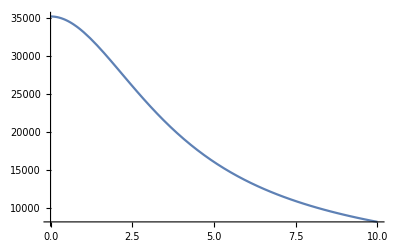

```mathematica
Plot[VE/.{α->alphaPt,A->APt,ϵ->1,R->r},{r,0,10}]
```

```mathematica
(*O-O interaction*)
```

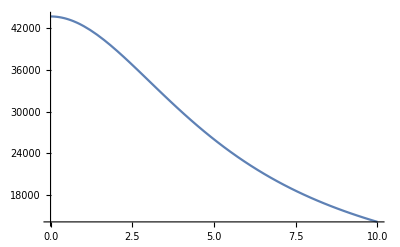

```mathematica
Plot[VE/.{α->alphaO,A->AO,ϵ->1,R->r},{r,0,10},PlotRange->All]
```

```mathematica
(*O-Pt interactions*)
```

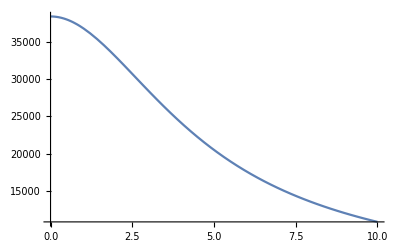

```mathematica
Plot[V/.{α->alphaPt,A->APt,ϵ->1,R->r,β->alphaO,B->AO},{r,0,10}]
```

```mathematica
VE
```

(A^2 ⅇ^(-R α) π (-48+48 ⅇ^(R α)-33 R α-9 R^2 α^2-R^3 α^3))/(3 R α^6 ϵ)

```mathematica
vp = D[VE,R] /. R->Rc
```

{(ⅇ^(-Rc α) (-33 α+48 ⅇ^(Rc α) α-18 Rc α^2-3 Rc^2 α^3))/(48 Rc)-(ⅇ^(-Rc α) (-48+48 ⅇ^(Rc α)-33 Rc α-9 Rc^2 α^2-Rc^3 α^3))/(48 Rc^2)-(ⅇ^(-Rc α) α (-48+48 ⅇ^(Rc α)-33 Rc α-9 Rc^2 α^2-Rc^3 α^3))/(48 Rc)}

```mathematica
sp = VE - (VE/. R->Rc)
```

{(ⅇ^(-R α) (-48+48 ⅇ^(R α)-33 R α-9 R^2 α^2-R^3 α^3))/(48 R)-(ⅇ^(-Rc α) (-48+48 ⅇ^(Rc α)-33 Rc α-9 Rc^2 α^2-Rc^3 α^3))/(48 Rc)}

```mathematica
sf = sp - vp * (R-Rc)
```

{(ⅇ^(-R α) (-48+48 ⅇ^(R α)-33 R α-9 R^2 α^2-R^3 α^3))/(48 R)-(ⅇ^(-Rc α) (-48+48 ⅇ^(Rc α)-33 Rc α-9 Rc^2 α^2-Rc^3 α^3))/(48 Rc)-(R-Rc) ((ⅇ^(-Rc α) (-33 α+48 ⅇ^(Rc α) α-18 Rc α^2-3 Rc^2 α^3))/(48 Rc)-(ⅇ^(-Rc α) (-48+48 ⅇ^(Rc α)-33 Rc α-9 Rc^2 α^2-Rc^3 α^3))/(48 Rc^2)-(ⅇ^(-Rc α) α (-48+48 ⅇ^(Rc α)-33 Rc α-9 Rc^2 α^2-Rc^3 α^3))/(48 Rc))}

```mathematica
V0=Limit[V,{R->0}]
```

{(α β (α^2+3 α β+β^2))/(2 (α+β)^3)}

```mathematica
VE0=V0/.{β->α}
```

{(5 α)/16}